# Root-shoot model: fast dynamics alone

#### Code for Timescale separation in models of symbiosis: state space reduction, multiple attractors and initialization (Pfab et al)

```mathematica
(*parameter*)
S=2;
R=1;
αC=1;
αN=1;
ηS=.2;
ηR=1;
αC=1;
αN=1;
λ=100;
(*equations*)
(*assimilation rates*)
UN=αN R;
UC=αC S;
(*SU*)
F[x_,y_]:=Min[x,y];
(*growth rate of root and shoot*)
dRdt=F[ρC ,UN/ηR];
dSdt=F[UC,ρN/ηS];
(*N and C shared (unbuffered)*)
gρN=UN-ηR dRdt;
gρC=UC-dSdt;
(*state variables: just fast state variables*)
vars={ρN,ρC};
(*directions of ρN and ρC*)
vρN=λ (gρN-ρN);
vρC=λ (gρC-ρC);
(*find equilibria*)
TableForm[eqs=Quiet@NSolve[{vρN==0,vρC==0},vars]]
```

ρN→0. | ρC→2.
ρN→0.25 | ρC→0.75
ρN→1. | ρC→0

```mathematica
(*eigenvector and eigenvalue analysis*)
JacobianMatrix[f_,x_]:=Outer[D,f,x];
(*the middle equilibrium - we want the separatrix which goes through this equilibrium*)
eq=eqs[[2]];
eigensystem=Eigensystem[JacobianMatrix[{vρN,vρC},vars]/.eq];
Grid[Table[{"eigenvalue :",eigensystem[[1,i]],"eigenvector :",MatrixForm[eigensystem[[2,i]]]},{i,Length@eigensystem[[1]]}]]
```

eigenvalue : | -323.607 | eigenvector : | (0.408248
0.912871)
eigenvalue : | 123.607 | eigenvector : | (0.408248
-0.912871)

```mathematica
(*the eigenvector with the smalles eigenvalue*)
eigenvec=Re@eigensystem[[2,Ordering[eigensystem[[1]],1][[1]]]]
```

{0.408248,0.912871}

```mathematica
(*run fast dynamics backwards in time to get separatrix, start in direction of eigenvalue found before*)
tminsep=-10;tmaxsep=0;ϵ=-.0001;
dosol[ϵ_]:=Quiet@NDSolve[#[[1]]==(#[[2]]/.((#->#[t])&/@vars))&/@{
ρN'[t]==vρN,
ρC'[t]==vρC,
ρN[0]==(ρN/.eq)+ϵ eigenvec[[1]],
ρC[0]==(ρC/.eq)+ϵ eigenvec[[2]]
},
vars,
{t,tminsep,tmaxsep}][[1]];
sol1=dosol[ϵ];
sol2=dosol[-ϵ];
```

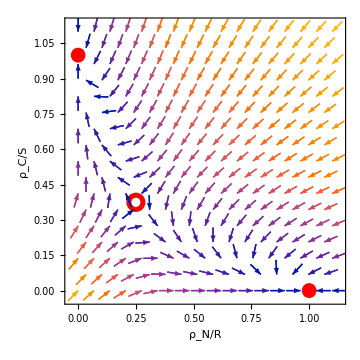

```mathematica
(*plot*)
fontfamily="Times";
(Export[NotebookDirectory[]<>"root-shoot-fast-dynamics-plane.pdf",#];#)&@Show[{
VectorPlot[{vρN/R, vρC/S}/.{ρN->ρNoverR R,ρC->ρCoverS S}, {ρNoverR,0,1.1},{ρCoverS,0,1.1},VectorPoints->17,FrameLabel->{"ρ_N/R","ρ_C/S"},Epilog->Join[{PointSize[.04],Red},Table[Piecewise[{{{Thickness[.01],Circle[#,Scaled@.025]}&, i==2}, {Disk[#,Scaled@.026]&, True}}]@{ρN/R,ρC/S}/.eqs[[i]],{i,Length@eqs}]],ImageSize->Medium,VectorMarkers->Placed["Arrow","End"]],
ParametricPlot[{{ρN[t]/R,ρC[t]/S}/.sol1,{ρN[t]/R,ρC[t]/S}/.sol2},{t,tminsep,tmaxsep},PlotStyle->{{Thickness[.015],Black}}]
},LabelStyle->{16,FontFamily->fontfamily}]
```